```mathematica
Clear[f]
```

```mathematica
f[w1_,w2_,w3_,x_]=w1 Exp[-(x-2)^2]+w2 Exp[-(x-3)^2]+w3 Exp[-(x-4)^2]
```

ⅇ^(-(-2+x)^2) w1+ⅇ^(-(-3+x)^2) w2+ⅇ^(-(-4+x)^2) w3

```mathematica
Manipulate[Plot[Exp[-f[w1,w2,w3,x]],{x,0,6},PlotRange->{0,1}],{w1,-1,+1},{w2,-1,+1},{w3,-1,+1}]
```

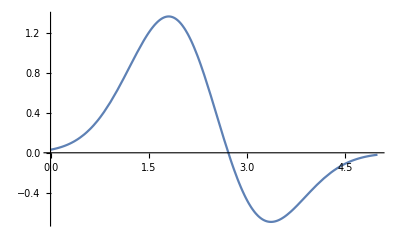

```mathematica
{t1,t2,t3} = {w1,w2,w3} /. Solve[{f[w1,w2,w3,1]==.6,f[w1,w2,w3,4]==.5,f[w1,w2,w3,5]==.3},{w1,w2,w3}][[1]];
Plot[f[t1,t2,0,x],{x,0,5}]
```

```mathematica
DynamicModule[{p={.8,.3}},
c11=p[[1]];
c12=p[[2]];
(*{t1,t2,t3} = {w1,w2,w3} /. Solve[{f[w1,w2,w3,c11]==c12,f[w1,w2,w3,4]==.5,f[w1,w2,w3,5]==.3},{w1,w2,w3}][[1]];*)
{t1}={w1} /. Solve[{f[w1,0,0,c11]==c12},{w1}];
{Dynamic[c11],Show[Graphics[Locator[Dynamic[p]]],Plot[f[1,2,3,x],{x,0,5}]],Dynamic[p]}]
```

```mathematica
Dynamic[t1]
```

```mathematica
t1//N
```

{1.26621}

```mathematica
FullForm[t1]
```

List[1.26621]

```mathematica
c1
```

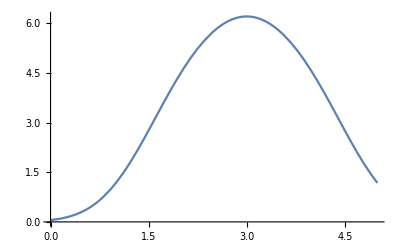

```mathematica
Plot[f[3,4,3,x],{x,0,5}]
```

```mathematica
Dynamic[({t1,t2,t3}//N)[[1]]]
```

```mathematica
c1
```

```mathematica
t1
```

-(1. (-0.101206 ⅇ^(-1. (-4.+)^2)+0.11606 ⅇ^(-1. (-3.+)^2)+0.11702 ))/(-0.000290063 ⅇ^(-1. (-4.+)^2)+0.00661454 ⅇ^(-1. (-3.+)^2)-0.11702 ⅇ^(-1. (-2.+)^2))

```mathematica
Manipulate[
{t1,t2,t3} = {w1,w2,w3} /. Solve[{f[w1,w2,w3,p1[[1]]]==-Log[p1[[2]]],f[w1,w2,w3,p2[[1]]]==-Log[p2[[2]]],f[w1,w2,w3,p3[[1]]]==-Log[p3[[2]]]},{w1,w2,w3}][[1]];
Graphics[
Plot[Exp[-f[t1,t2,t3,x]],{x,0,6},PlotRange->{0,5}]
],
{{p1,{2,1}},Locator},
{{p2,{3,1}},Locator},
{{p3,{4,1}},Locator}
]
```